# A file from 1985

### Initialization

```mathematica
Off[General::spell,General::spell1]
```

### Function to expand bytes into bits

```mathematica
ByteExpand=Function[{byte},Sign[BitAnd[byte,#]]&/@Table[2^b,{b,7,0,-1}]]
```

Function[{byte},(Sign[BitAnd[byte,#1]]&)/@Table[2^b,{b,7,0,-1}]]

### Function to compress bit array into words

```mathematica
WordBuild=Function[{bitarray},Fold[2#1+#2&,0,bitarray]]
```

Function[{bitarray},Fold[2 #1+#2&,0,bitarray]]

## Import raw data from file

```mathematica
SetDirectory["."]
```

/home/cmaier/Zeit/Ananthaswamy-Lesekreis/BildGPT

```mathematica
rawdata=Import["tinyfont1985.txt","Lines"];
Dimensions[rawdata]
```

{95}

```mathematica
rawdatastrings=StringSplit/@rawdata;
Dimensions[rawdatastrings]
```

{95,10}

```mathematica
datawords=Drop[#,-1]&/@Map[ToExpression["16^^"<>#]&,rawdatastrings,{-1}];
Dimensions[datawords]
```

{95,9}

```mathematica
Export["binaryfile.raw",Flatten[datawords],"Binary"]
```

binaryfile.raw

```mathematica
datamatrices=Map[ByteExpand,datawords,{-1}];
Dimensions[datamatrices]
```

{95,9,8}

```mathematica
rasters=Map[Graphics[Raster[#],Frame->True,FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),AspectRatio->1.2]&,Map[Reverse,datamatrices,{1}],{1}];
```

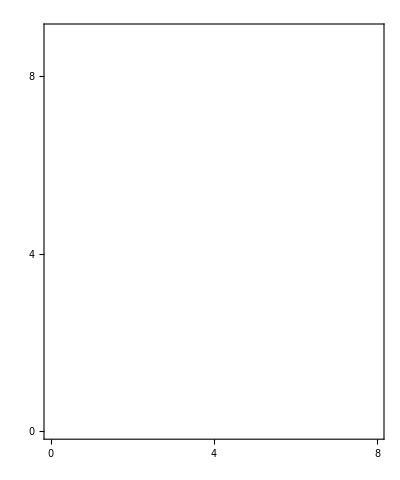
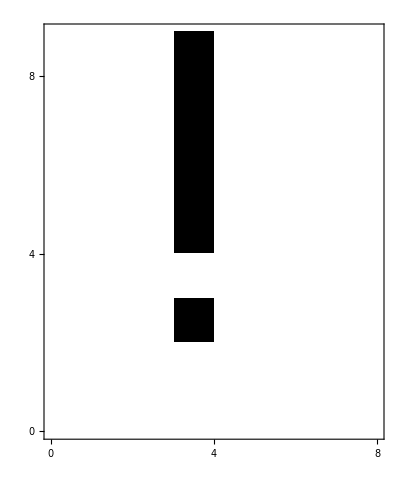
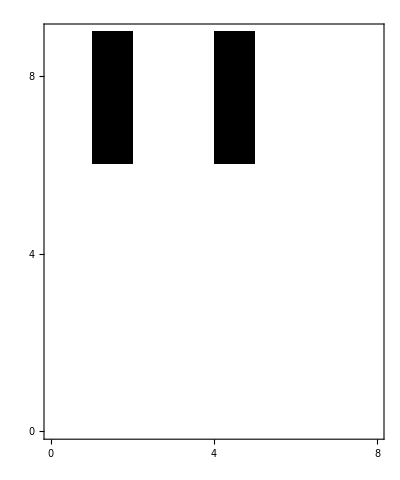
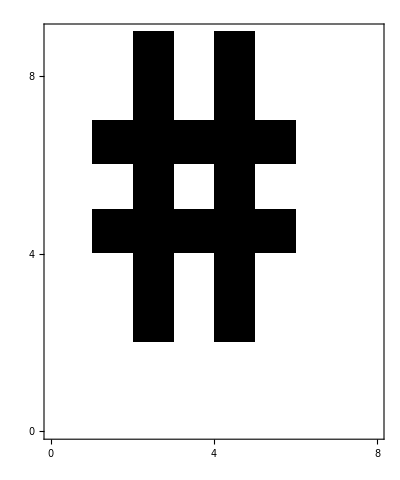
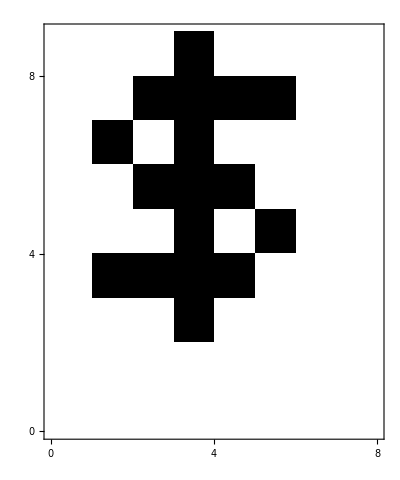
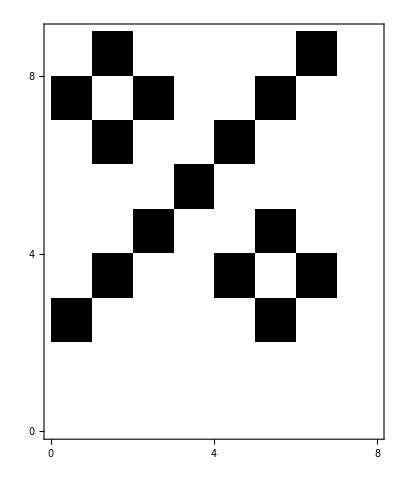
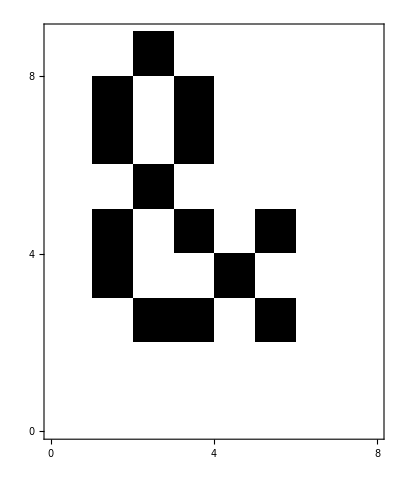
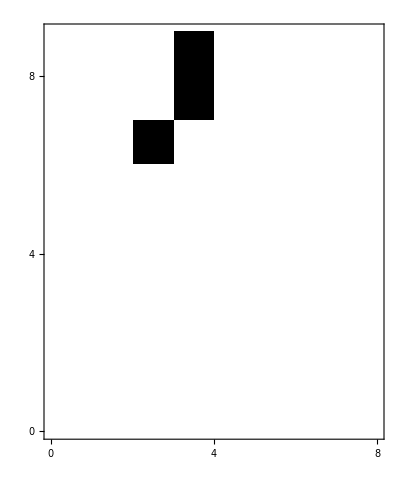

```mathematica
Show/@rasters
```

## Convert font to Navitrack LCD format

```mathematica
expandedmatrices={Reverse[#],1-Reverse[#]}&/@Map[Join[#,Table[1,{b,16Ceiling[Length[#]/16]-Length[#]}]]&,datamatrices,{-2}];
Dimensions[expandedmatrices]
```

{95,2,9,16}

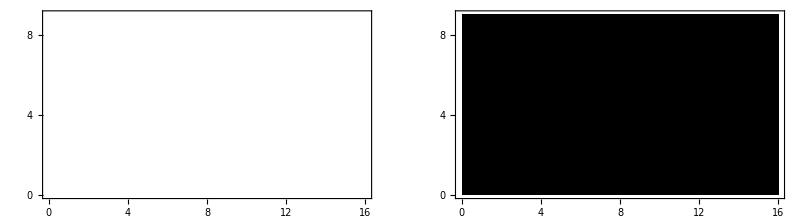
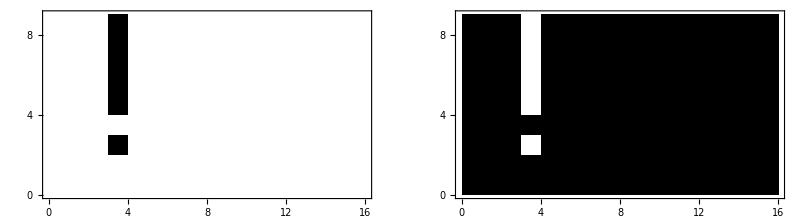
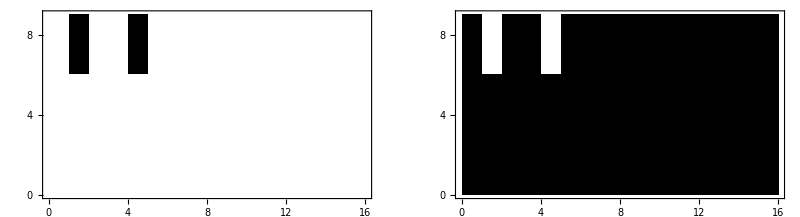
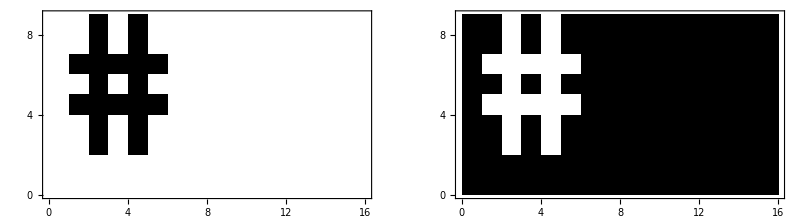
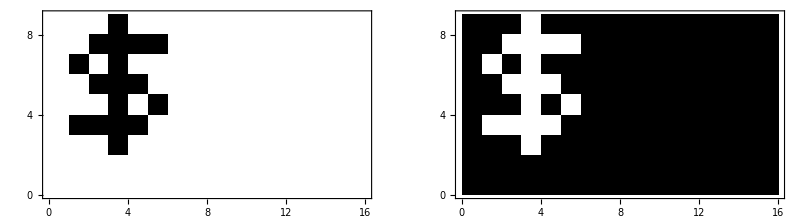
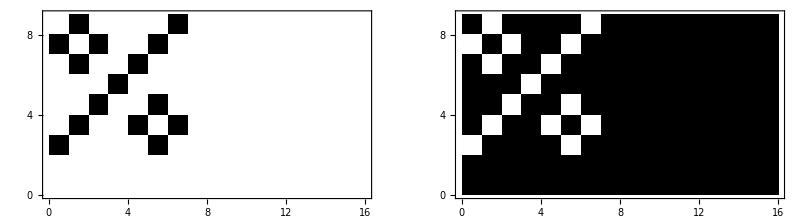
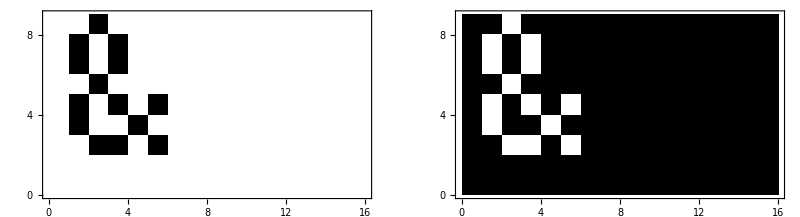
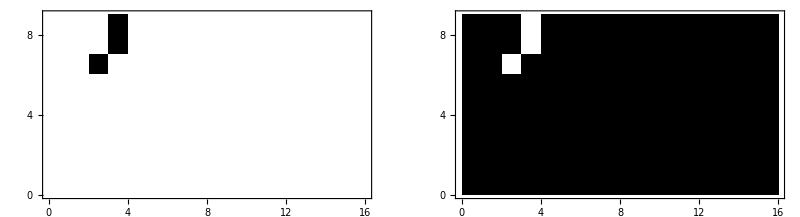
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Graphics[Raster[#],Frame->True,FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),AspectRatio->9/16]&,expandedmatrices,{2}];
Show[GraphicsGrid[{#}]]&/@%
```

```mathematica
outputbitmasks=Map[WordBuild,expandedmatrices,{-2}];
outputcharacters=Map[Flatten[{{9,7},#1}]&,outputbitmasks];
Dimensions[outputcharacters]
```

{95,20}

```mathematica
Export["binaryfeile.raw",Flatten[outputcharacters],"UnsignedInteger16"]
```

binaryfeile.raw

### Send data function

```mathematica
SaveCharacterFile=Function[{filename,data},
Block[{stream=OpenWrite[filename],headertemplate="1651 1 0 1 "},
Write[stream,OutputForm[#]]&/@
Prepend["0x"<>StringSplit[ToString[BaseForm[#,16]]]⟦1⟧&/@data,headertemplate<>ToString[Length[data]]];
Close[stream]]
]
```

Function[{filename,data},Block[{stream=OpenWrite[filename],headertemplate=1651 1 0 1 },(Write[stream,#1]&)/@Prepend[(0x<>StringSplit[ToString[Slot[1_16]]]⟦1⟧&)/@data,headertemplate<>ToString[Length[data]]];Close[stream]]]

### Organize the font by individual character files

#### Define file names for individual character .dat2 files

```mathematica
outputcharacternames="tinyfont1985_ASCII_0x"<>StringSplit[ToString[BaseForm[#,16]]]⟦1⟧<>".dat2"&/@(Range@@ToCharacterCode[" ~"])
```

{tinyfont1985_ASCII_0x20.dat2,tinyfont1985_ASCII_0x21.dat2,tinyfont1985_ASCII_0x22.dat2,tinyfont1985_ASCII_0x23.dat2,tinyfont1985_ASCII_0x24.dat2,tinyfont1985_ASCII_0x25.dat2,tinyfont1985_ASCII_0x26.dat2,tinyfont1985_ASCII_0x27.dat2,tinyfont1985_ASCII_0x28.dat2,tinyfont1985_ASCII_0x29.dat2,tinyfont1985_ASCII_0x2a.dat2,tinyfont1985_ASCII_0x2b.dat2,tinyfont1985_ASCII_0x2c.dat2,tinyfont1985_ASCII_0x2d.dat2,tinyfont1985_ASCII_0x2e.dat2,tinyfont1985_ASCII_0x2f.dat2,tinyfont1985_ASCII_0x30.dat2,tinyfont1985_ASCII_0x31.dat2,tinyfont1985_ASCII_0x32.dat2,tinyfont1985_ASCII_0x33.dat2,tinyfont1985_ASCII_0x34.dat2,tinyfont1985_ASCII_0x35.dat2,tinyfont1985_ASCII_0x36.dat2,tinyfont1985_ASCII_0x37.dat2,tinyfont1985_ASCII_0x38.dat2,tinyfont1985_ASCII_0x39.dat2,tinyfont1985_ASCII_0x3a.dat2,tinyfont1985_ASCII_0x3b.dat2,tinyfont1985_ASCII_0x3c.dat2,tinyfont1985_ASCII_0x3d.dat2,tinyfont1985_ASCII_0x3e.dat2,tinyfont1985_ASCII_0x3f.dat2,tinyfont1985_ASCII_0x40.dat2,tinyfont1985_ASCII_0x41.dat2,tinyfont1985_ASCII_0x42.dat2,tinyfont1985_ASCII_0x43.dat2,tinyfont1985_ASCII_0x44.dat2,tinyfont1985_ASCII_0x45.dat2,tinyfont1985_ASCII_0x46.dat2,tinyfont1985_ASCII_0x47.dat2,tinyfont1985_ASCII_0x48.dat2,tinyfont1985_ASCII_0x49.dat2,tinyfont1985_ASCII_0x4a.dat2,tinyfont1985_ASCII_0x4b.dat2,tinyfont1985_ASCII_0x4c.dat2,tinyfont1985_ASCII_0x4d.dat2,tinyfont1985_ASCII_0x4e.dat2,tinyfont1985_ASCII_0x4f.dat2,tinyfont1985_ASCII_0x50.dat2,tinyfont1985_ASCII_0x51.dat2,tinyfont1985_ASCII_0x52.dat2,tinyfont1985_ASCII_0x53.dat2,tinyfont1985_ASCII_0x54.dat2,tinyfont1985_ASCII_0x55.dat2,tinyfont1985_ASCII_0x56.dat2,tinyfont1985_ASCII_0x57.dat2,tinyfont1985_ASCII_0x58.dat2,tinyfont1985_ASCII_0x59.dat2,tinyfont1985_ASCII_0x5a.dat2,tinyfont1985_ASCII_0x5b.dat2,tinyfont1985_ASCII_0x5c.dat2,tinyfont1985_ASCII_0x5d.dat2,tinyfont1985_ASCII_0x5e.dat2,tinyfont1985_ASCII_0x5f.dat2,tinyfont1985_ASCII_0x60.dat2,tinyfont1985_ASCII_0x61.dat2,tinyfont1985_ASCII_0x62.dat2,tinyfont1985_ASCII_0x63.dat2,tinyfont1985_ASCII_0x64.dat2,tinyfont1985_ASCII_0x65.dat2,tinyfont1985_ASCII_0x66.dat2,tinyfont1985_ASCII_0x67.dat2,tinyfont1985_ASCII_0x68.dat2,tinyfont1985_ASCII_0x69.dat2,tinyfont1985_ASCII_0x6a.dat2,tinyfont1985_ASCII_0x6b.dat2,tinyfont1985_ASCII_0x6c.dat2,tinyfont1985_ASCII_0x6d.dat2,tinyfont1985_ASCII_0x6e.dat2,tinyfont1985_ASCII_0x6f.dat2,tinyfont1985_ASCII_0x70.dat2,tinyfont1985_ASCII_0x71.dat2,tinyfont1985_ASCII_0x72.dat2,tinyfont1985_ASCII_0x73.dat2,tinyfont1985_ASCII_0x74.dat2,tinyfont1985_ASCII_0x75.dat2,tinyfont1985_ASCII_0x76.dat2,tinyfont1985_ASCII_0x77.dat2,tinyfont1985_ASCII_0x78.dat2,tinyfont1985_ASCII_0x79.dat2,tinyfont1985_ASCII_0x7a.dat2,tinyfont1985_ASCII_0x7b.dat2,tinyfont1985_ASCII_0x7c.dat2,tinyfont1985_ASCII_0x7d.dat2,tinyfont1985_ASCII_0x7e.dat2}

#### Define variable names for individual character bit maps

```mathematica
outputcharactervariables="tinyfont1985_ascii_0x"<>StringSplit[ToString[BaseForm[#,16]]]⟦1⟧<>"_addr"&/@(Range@@ToCharacterCode[" ~"])
```

{tinyfont1985_ascii_0x20_addr,tinyfont1985_ascii_0x21_addr,tinyfont1985_ascii_0x22_addr,tinyfont1985_ascii_0x23_addr,tinyfont1985_ascii_0x24_addr,tinyfont1985_ascii_0x25_addr,tinyfont1985_ascii_0x26_addr,tinyfont1985_ascii_0x27_addr,tinyfont1985_ascii_0x28_addr,tinyfont1985_ascii_0x29_addr,tinyfont1985_ascii_0x2a_addr,tinyfont1985_ascii_0x2b_addr,tinyfont1985_ascii_0x2c_addr,tinyfont1985_ascii_0x2d_addr,tinyfont1985_ascii_0x2e_addr,tinyfont1985_ascii_0x2f_addr,tinyfont1985_ascii_0x30_addr,tinyfont1985_ascii_0x31_addr,tinyfont1985_ascii_0x32_addr,tinyfont1985_ascii_0x33_addr,tinyfont1985_ascii_0x34_addr,tinyfont1985_ascii_0x35_addr,tinyfont1985_ascii_0x36_addr,tinyfont1985_ascii_0x37_addr,tinyfont1985_ascii_0x38_addr,tinyfont1985_ascii_0x39_addr,tinyfont1985_ascii_0x3a_addr,tinyfont1985_ascii_0x3b_addr,tinyfont1985_ascii_0x3c_addr,tinyfont1985_ascii_0x3d_addr,tinyfont1985_ascii_0x3e_addr,tinyfont1985_ascii_0x3f_addr,tinyfont1985_ascii_0x40_addr,tinyfont1985_ascii_0x41_addr,tinyfont1985_ascii_0x42_addr,tinyfont1985_ascii_0x43_addr,tinyfont1985_ascii_0x44_addr,tinyfont1985_ascii_0x45_addr,tinyfont1985_ascii_0x46_addr,tinyfont1985_ascii_0x47_addr,tinyfont1985_ascii_0x48_addr,tinyfont1985_ascii_0x49_addr,tinyfont1985_ascii_0x4a_addr,tinyfont1985_ascii_0x4b_addr,tinyfont1985_ascii_0x4c_addr,tinyfont1985_ascii_0x4d_addr,tinyfont1985_ascii_0x4e_addr,tinyfont1985_ascii_0x4f_addr,tinyfont1985_ascii_0x50_addr,tinyfont1985_ascii_0x51_addr,tinyfont1985_ascii_0x52_addr,tinyfont1985_ascii_0x53_addr,tinyfont1985_ascii_0x54_addr,tinyfont1985_ascii_0x55_addr,tinyfont1985_ascii_0x56_addr,tinyfont1985_ascii_0x57_addr,tinyfont1985_ascii_0x58_addr,tinyfont1985_ascii_0x59_addr,tinyfont1985_ascii_0x5a_addr,tinyfont1985_ascii_0x5b_addr,tinyfont1985_ascii_0x5c_addr,tinyfont1985_ascii_0x5d_addr,tinyfont1985_ascii_0x5e_addr,tinyfont1985_ascii_0x5f_addr,tinyfont1985_ascii_0x60_addr,tinyfont1985_ascii_0x61_addr,tinyfont1985_ascii_0x62_addr,tinyfont1985_ascii_0x63_addr,tinyfont1985_ascii_0x64_addr,tinyfont1985_ascii_0x65_addr,tinyfont1985_ascii_0x66_addr,tinyfont1985_ascii_0x67_addr,tinyfont1985_ascii_0x68_addr,tinyfont1985_ascii_0x69_addr,tinyfont1985_ascii_0x6a_addr,tinyfont1985_ascii_0x6b_addr,tinyfont1985_ascii_0x6c_addr,tinyfont1985_ascii_0x6d_addr,tinyfont1985_ascii_0x6e_addr,tinyfont1985_ascii_0x6f_addr,tinyfont1985_ascii_0x70_addr,tinyfont1985_ascii_0x71_addr,tinyfont1985_ascii_0x72_addr,tinyfont1985_ascii_0x73_addr,tinyfont1985_ascii_0x74_addr,tinyfont1985_ascii_0x75_addr,tinyfont1985_ascii_0x76_addr,tinyfont1985_ascii_0x77_addr,tinyfont1985_ascii_0x78_addr,tinyfont1985_ascii_0x79_addr,tinyfont1985_ascii_0x7a_addr,tinyfont1985_ascii_0x7b_addr,tinyfont1985_ascii_0x7c_addr,tinyfont1985_ascii_0x7d_addr,tinyfont1985_ascii_0x7e_addr}

```mathematica
SetDirectory["//Celsius/USERS/Christoph_Maier/VersionControl/ChristophsPlayground/Locator_Projects/DSP/Shared_Dev/Common_Code/Resources/LCD_AT320240/Dat_Files/font"]
```

\\Celsius\USERS\Christoph_Maier\VersionControl\ChristophsPlayground\Locator_Projects\DSP\Shared_Dev\Common_Code\Resources\LCD_AT320240\Dat_Files\font

```mathematica
Dimensions[outputcharacters]
```

{95,20}

```mathematica
outputcharacters
```

{{9,7,65535,65535,65535,65535,65535,65535,65535,65535,65535,0,0,0,0,0,0,0,0,0},{9,7,65535,65535,61439,65535,61439,61439,61439,61439,61439,0,0,4096,0,4096,4096,4096,4096,4096},{9,7,65535,65535,65535,65535,65535,65535,47103,47103,47103,0,0,0,0,0,0,18432,18432,18432},{9,7,65535,65535,55295,55295,33791,55295,33791,55295,55295,0,0,10240,10240,31744,10240,31744,10240,10240},{9,7,65535,65535,61439,34815,60415,51199,45055,50175,61439,0,0,4096,30720,5120,14336,20480,15360,4096},{9,7,65535,65535,31743,46591,56319,61439,47103,23551,48639,0,0,33792,18944,9216,4096,18432,41984,16896},{9,7,65535,65535,52223,47103,44031,57343,45055,45055,57343,0,0,13312,18432,21504,8192,20480,20480,8192},{9,7,65535,65535,65535,65535,65535,65535,57343,61439,61439,0,0,0,0,0,0,8192,4096,4096},{9,7,65535,65535,63487,61439,57343,57343,57343,61439,63487,0,0,2048,4096,8192,8192,8192,4096,2048},{9,7,65535,65535,57343,61439,63487,63487,63487,61439,57343,0,0,8192,4096,2048,2048,2048,4096,8192},{9,7,65535,65535,55295,61439,33791,61439,55295,65535,65535,0,0,10240,4096,31744,4096,10240,0,0},{9,7,65535,65535,61439,61439,33791,61439,61439,65535,65535,0,0,4096,4096,31744,4096,4096,0,0},{9,7,65535,57343,61439,61439,65535,65535,65535,65535,65535,0,8192,4096,4096,0,0,0,0,0},{9,7,65535,65535,65535,65535,33791,65535,65535,65535,65535,0,0,0,0,31744,0,0,0,0},{9,7,65535,65535,53247,53247,65535,65535,65535,65535,65535,0,0,12288,12288,0,0,0,0,0},{9,7,65535,65535,49151,49151,57343,61439,63487,64511,64511,0,0,16384,16384,8192,4096,2048,1024,1024},{9,7,65535,65535,51199,48127,39935,44031,46079,48127,51199,0,0,14336,17408,25600,21504,19456,17408,14336},{9,7,65535,65535,58367,63487,63487,63487,55295,59391,63487,0,0,7168,2048,2048,2048,10240,6144,2048},{9,7,65535,65535,33791,57343,61439,63487,64511,48127,51199,0,0,31744,8192,4096,2048,1024,17408,14336},{9,7,65535,65535,51199,48127,64511,59391,64511,48127,51199,0,0,14336,17408,1024,6144,1024,17408,14336},{9,7,65535,65535,63487,63487,33791,47103,55295,59391,63487,0,0,2048,2048,31744,18432,10240,6144,2048},{9,7,65535,65535,51199,48127,64511,34815,49151,49151,33791,0,0,14336,17408,1024,30720,16384,16384,31744},{9,7,65535,65535,51199,48127,48127,34815,49151,48127,51199,0,0,14336,17408,17408,30720,16384,17408,14336},{9,7,65535,65535,57343,57343,57343,61439,63487,64511,33791,0,0,8192,8192,8192,4096,2048,1024,31744},{9,7,65535,65535,51199,48127,48127,51199,48127,48127,51199,0,0,14336,17408,17408,14336,17408,17408,14336},{9,7,65535,65535,51199,48127,64511,50175,48127,48127,51199,0,0,14336,17408,1024,15360,17408,17408,14336},{9,7,65535,65535,53247,53247,65535,53247,53247,65535,65535,0,0,12288,12288,0,12288,12288,0,0},{9,7,65535,57343,61439,61439,65535,53247,53247,65535,65535,0,8192,4096,4096,0,12288,12288,0,0},{9,7,65535,65535,63487,61439,57343,61439,63487,65535,65535,0,0,2048,4096,8192,4096,2048,0,0},{9,7,65535,65535,65535,33791,65535,33791,65535,65535,65535,0,0,0,31744,0,31744,0,0,0},{9,7,65535,65535,57343,61439,63487,61439,57343,65535,65535,0,0,8192,4096,2048,4096,8192,0,0},{9,7,65535,65535,61439,65535,61439,61439,63487,48127,51199,0,0,4096,0,4096,4096,2048,17408,14336},{9,7,65535,65535,49151,27647,22015,22015,28159,48127,51199,0,0,16384,37888,43520,43520,37376,17408,14336},{9,7,65535,65535,48127,48127,33791,48127,48127,55295,61439,0,0,17408,17408,31744,17408,17408,10240,4096},{9,7,65535,65535,34815,48127,48127,34815,48127,48127,34815,0,0,30720,17408,17408,30720,17408,17408,30720},{9,7,65535,65535,51199,48127,49151,49151,49151,48127,51199,0,0,14336,17408,16384,16384,16384,17408,14336},{9,7,65535,65535,36863,47103,48127,48127,48127,47103,36863,0,0,28672,18432,17408,17408,17408,18432,28672},{9,7,65535,65535,33791,49151,49151,34815,49151,49151,33791,0,0,31744,16384,16384,30720,16384,16384,31744},{9,7,65535,65535,49151,49151,49151,34815,49151,49151,33791,0,0,16384,16384,16384,30720,16384,16384,31744},{9,7,65535,65535,51199,48127,48127,41983,49151,48127,51199,0,0,14336,17408,17408,23552,16384,17408,14336},{9,7,65535,65535,48127,48127,48127,33791,48127,48127,48127,0,0,17408,17408,17408,31744,17408,17408,17408},{9,7,65535,65535,51199,61439,61439,61439,61439,61439,51199,0,0,14336,4096,4096,4096,4096,4096,14336},{9,7,65535,65535,51199,48127,64511,64511,64511,64511,64511,0,0,14336,17408,1024,1024,1024,1024,1024},{9,7,65535,65535,48127,47103,45055,40959,45055,47103,48127,0,0,17408,18432,20480,24576,20480,18432,17408},{9,7,65535,65535,33791,49151,49151,49151,49151,49151,49151,0,0,31744,16384,16384,16384,16384,16384,16384},{9,7,65535,65535,48127,48127,48127,44031,44031,37887,48127,0,0,17408,17408,17408,21504,21504,27648,17408},{9,7,65535,65535,48127,48127,46079,44031,39935,48127,48127,0,0,17408,17408,19456,21504,25600,17408,17408},{9,7,65535,65535,51199,48127,48127,48127,48127,48127,51199,0,0,14336,17408,17408,17408,17408,17408,14336},{9,7,65535,65535,49151,49151,49151,34815,48127,48127,34815,0,0,16384,16384,16384,30720,17408,17408,30720},{9,7,65535,65535,52223,47103,44031,48127,48127,48127,51199,0,0,13312,18432,21504,17408,17408,17408,14336},{9,7,65535,65535,47103,45055,40959,34815,48127,48127,34815,0,0,18432,20480,24576,30720,17408,17408,30720},{9,7,65535,65535,34815,64511,64511,51199,49151,49151,50175,0,0,30720,1024,1024,14336,16384,16384,15360},{9,7,65535,65535,61439,61439,61439,61439,61439,61439,33791,0,0,4096,4096,4096,4096,4096,4096,31744},{9,7,65535,65535,51199,48127,48127,48127,48127,48127,48127,0,0,14336,17408,17408,17408,17408,17408,17408},{9,7,65535,65535,61439,55295,48127,48127,48127,48127,48127,0,0,4096,10240,17408,17408,17408,17408,17408},{9,7,65535,65535,55295,44031,44031,44031,48127,48127,48127,0,0,10240,21504,21504,21504,17408,17408,17408},{9,7,65535,65535,48127,48127,55295,61439,55295,48127,48127,0,0,17408,17408,10240,4096,10240,17408,17408},{9,7,65535,65535,61439,61439,61439,61439,55295,48127,48127,0,0,4096,4096,4096,4096,10240,17408,17408},{9,7,65535,65535,33791,49151,57343,61439,63487,64511,33791,0,0,31744,16384,8192,4096,2048,1024,31744},{9,7,65535,65535,51199,57343,57343,57343,57343,57343,51199,0,0,14336,8192,8192,8192,8192,8192,14336},{9,7,65535,65535,64511,64511,63487,61439,57343,49151,49151,0,0,1024,1024,2048,4096,8192,16384,16384},{9,7,65535,65535,51199,63487,63487,63487,63487,63487,51199,0,0,14336,2048,2048,2048,2048,2048,14336},{9,7,65535,65535,65535,65535,48127,55295,61439,65535,65535,0,0,0,0,17408,10240,4096,0,0},{9,7,65535,511,65535,65535,65535,65535,65535,65535,65535,0,65024,0,0,0,0,0,0,0},{9,7,65535,65535,65535,65535,65535,65535,63487,61439,61439,0,0,0,0,0,0,2048,4096,4096},{9,7,65535,65535,50175,48127,50175,64511,34815,65535,65535,0,0,15360,17408,15360,1024,30720,0,0},{9,7,65535,65535,34815,48127,48127,48127,34815,49151,49151,0,0,30720,17408,17408,17408,30720,16384,16384},{9,7,65535,65535,50175,49151,49151,49151,50175,65535,65535,0,0,15360,16384,16384,16384,15360,0,0},{9,7,65535,65535,50175,48127,48127,48127,50175,64511,64511,0,0,15360,17408,17408,17408,15360,1024,1024},{9,7,65535,65535,50175,49151,33791,48127,51199,65535,65535,0,0,15360,16384,31744,17408,14336,0,0},{9,7,65535,65535,57343,57343,57343,34815,57343,56319,59391,0,0,8192,8192,8192,30720,8192,9216,6144},{9,7,34815,64511,50175,48127,48127,48127,50175,65535,65535,30720,1024,15360,17408,17408,17408,15360,0,0},{9,7,65535,65535,48127,48127,48127,48127,34815,49151,49151,0,0,17408,17408,17408,17408,30720,16384,16384},{9,7,65535,65535,51199,61439,61439,61439,53247,65535,61439,0,0,14336,4096,4096,4096,12288,0,4096},{9,7,61439,55295,63487,63487,63487,63487,59391,65535,63487,4096,10240,2048,2048,2048,2048,6144,0,2048},{9,7,65535,65535,47103,45055,40959,45055,47103,49151,49151,0,0,18432,20480,24576,20480,18432,16384,16384},{9,7,65535,65535,51199,61439,61439,61439,61439,61439,53247,0,0,14336,4096,4096,4096,4096,4096,12288},{9,7,65535,65535,44031,44031,44031,44031,38911,65535,65535,0,0,21504,21504,21504,21504,26624,0,0},{9,7,65535,65535,48127,48127,48127,48127,34815,65535,65535,0,0,17408,17408,17408,17408,30720,0,0},{9,7,65535,65535,51199,48127,48127,48127,51199,65535,65535,0,0,14336,17408,17408,17408,14336,0,0},{9,7,49151,49151,34815,48127,48127,48127,34815,65535,65535,16384,16384,30720,17408,17408,17408,30720,0,0},{9,7,64511,64511,50175,48127,48127,48127,50175,65535,65535,1024,1024,15360,17408,17408,17408,15360,0,0},{9,7,65535,65535,36863,57343,57343,56319,34815,65535,65535,0,0,28672,8192,8192,9216,30720,0,0},{9,7,65535,65535,34815,64511,51199,49151,50175,65535,65535,0,0,30720,1024,14336,16384,15360,0,0},{9,7,65535,65535,63487,61439,61439,61439,33791,61439,61439,0,0,2048,4096,4096,4096,31744,4096,4096},{9,7,65535,65535,51199,48127,48127,48127,48127,65535,65535,0,0,14336,17408,17408,17408,17408,0,0},{9,7,65535,65535,61439,55295,48127,48127,48127,65535,65535,0,0,4096,10240,17408,17408,17408,0,0},{9,7,65535,65535,55295,44031,44031,44031,44031,65535,65535,0,0,10240,21504,21504,21504,21504,0,0},{9,7,65535,65535,48127,55295,61439,55295,48127,65535,65535,0,0,17408,10240,4096,10240,17408,0,0},{9,7,34815,64511,50175,48127,48127,48127,48127,65535,65535,30720,1024,15360,17408,17408,17408,17408,0,0},{9,7,65535,65535,33791,57343,61439,63487,33791,65535,65535,0,0,31744,8192,4096,2048,31744,0,0},{9,7,65535,65535,63487,61439,61439,57343,61439,61439,63487,0,0,2048,4096,4096,8192,4096,4096,2048},{9,7,65535,65535,61439,61439,61439,61439,61439,61439,61439,0,0,4096,4096,4096,4096,4096,4096,4096},{9,7,65535,65535,57343,61439,61439,63487,61439,61439,57343,0,0,8192,4096,4096,2048,4096,4096,8192},{9,7,65535,65535,65535,65535,63487,44031,57343,65535,65535,0,0,0,0,2048,21504,8192,0,0}}

```mathematica
MapThread[SaveCharacterFile,{outputcharacternames,outputcharacters},1]
```

{tinyfont1985_ASCII_0x20.dat2,tinyfont1985_ASCII_0x21.dat2,tinyfont1985_ASCII_0x22.dat2,tinyfont1985_ASCII_0x23.dat2,tinyfont1985_ASCII_0x24.dat2,tinyfont1985_ASCII_0x25.dat2,tinyfont1985_ASCII_0x26.dat2,tinyfont1985_ASCII_0x27.dat2,tinyfont1985_ASCII_0x28.dat2,tinyfont1985_ASCII_0x29.dat2,tinyfont1985_ASCII_0x2a.dat2,tinyfont1985_ASCII_0x2b.dat2,tinyfont1985_ASCII_0x2c.dat2,tinyfont1985_ASCII_0x2d.dat2,tinyfont1985_ASCII_0x2e.dat2,tinyfont1985_ASCII_0x2f.dat2,tinyfont1985_ASCII_0x30.dat2,tinyfont1985_ASCII_0x31.dat2,tinyfont1985_ASCII_0x32.dat2,tinyfont1985_ASCII_0x33.dat2,tinyfont1985_ASCII_0x34.dat2,tinyfont1985_ASCII_0x35.dat2,tinyfont1985_ASCII_0x36.dat2,tinyfont1985_ASCII_0x37.dat2,tinyfont1985_ASCII_0x38.dat2,tinyfont1985_ASCII_0x39.dat2,tinyfont1985_ASCII_0x3a.dat2,tinyfont1985_ASCII_0x3b.dat2,tinyfont1985_ASCII_0x3c.dat2,tinyfont1985_ASCII_0x3d.dat2,tinyfont1985_ASCII_0x3e.dat2,tinyfont1985_ASCII_0x3f.dat2,tinyfont1985_ASCII_0x40.dat2,tinyfont1985_ASCII_0x41.dat2,tinyfont1985_ASCII_0x42.dat2,tinyfont1985_ASCII_0x43.dat2,tinyfont1985_ASCII_0x44.dat2,tinyfont1985_ASCII_0x45.dat2,tinyfont1985_ASCII_0x46.dat2,tinyfont1985_ASCII_0x47.dat2,tinyfont1985_ASCII_0x48.dat2,tinyfont1985_ASCII_0x49.dat2,tinyfont1985_ASCII_0x4a.dat2,tinyfont1985_ASCII_0x4b.dat2,tinyfont1985_ASCII_0x4c.dat2,tinyfont1985_ASCII_0x4d.dat2,tinyfont1985_ASCII_0x4e.dat2,tinyfont1985_ASCII_0x4f.dat2,tinyfont1985_ASCII_0x50.dat2,tinyfont1985_ASCII_0x51.dat2,tinyfont1985_ASCII_0x52.dat2,tinyfont1985_ASCII_0x53.dat2,tinyfont1985_ASCII_0x54.dat2,tinyfont1985_ASCII_0x55.dat2,tinyfont1985_ASCII_0x56.dat2,tinyfont1985_ASCII_0x57.dat2,tinyfont1985_ASCII_0x58.dat2,tinyfont1985_ASCII_0x59.dat2,tinyfont1985_ASCII_0x5a.dat2,tinyfont1985_ASCII_0x5b.dat2,tinyfont1985_ASCII_0x5c.dat2,tinyfont1985_ASCII_0x5d.dat2,tinyfont1985_ASCII_0x5e.dat2,tinyfont1985_ASCII_0x5f.dat2,tinyfont1985_ASCII_0x60.dat2,tinyfont1985_ASCII_0x61.dat2,tinyfont1985_ASCII_0x62.dat2,tinyfont1985_ASCII_0x63.dat2,tinyfont1985_ASCII_0x64.dat2,tinyfont1985_ASCII_0x65.dat2,tinyfont1985_ASCII_0x66.dat2,tinyfont1985_ASCII_0x67.dat2,tinyfont1985_ASCII_0x68.dat2,tinyfont1985_ASCII_0x69.dat2,tinyfont1985_ASCII_0x6a.dat2,tinyfont1985_ASCII_0x6b.dat2,tinyfont1985_ASCII_0x6c.dat2,tinyfont1985_ASCII_0x6d.dat2,tinyfont1985_ASCII_0x6e.dat2,tinyfont1985_ASCII_0x6f.dat2,tinyfont1985_ASCII_0x70.dat2,tinyfont1985_ASCII_0x71.dat2,tinyfont1985_ASCII_0x72.dat2,tinyfont1985_ASCII_0x73.dat2,tinyfont1985_ASCII_0x74.dat2,tinyfont1985_ASCII_0x75.dat2,tinyfont1985_ASCII_0x76.dat2,tinyfont1985_ASCII_0x77.dat2,tinyfont1985_ASCII_0x78.dat2,tinyfont1985_ASCII_0x79.dat2,tinyfont1985_ASCII_0x7a.dat2,tinyfont1985_ASCII_0x7b.dat2,tinyfont1985_ASCII_0x7c.dat2,tinyfont1985_ASCII_0x7d.dat2,tinyfont1985_ASCII_0x7e.dat2}

### Generate Flash programmer command file entry

```mathematica
MapThread["%LCD_AT320240_Dir%\\Dat_Files\\font\\"<>#1<>">"<>#2<>";"&,{outputcharacternames,outputcharactervariables}]
Export["commandfile.tinyfont1985.txt",%,"Lines"]
```

{%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x20.dat2>tinyfont1985_ascii_0x20_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x21.dat2>tinyfont1985_ascii_0x21_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x22.dat2>tinyfont1985_ascii_0x22_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x23.dat2>tinyfont1985_ascii_0x23_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x24.dat2>tinyfont1985_ascii_0x24_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x25.dat2>tinyfont1985_ascii_0x25_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x26.dat2>tinyfont1985_ascii_0x26_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x27.dat2>tinyfont1985_ascii_0x27_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x28.dat2>tinyfont1985_ascii_0x28_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x29.dat2>tinyfont1985_ascii_0x29_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x2a.dat2>tinyfont1985_ascii_0x2a_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x2b.dat2>tinyfont1985_ascii_0x2b_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x2c.dat2>tinyfont1985_ascii_0x2c_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x2d.dat2>tinyfont1985_ascii_0x2d_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x2e.dat2>tinyfont1985_ascii_0x2e_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x2f.dat2>tinyfont1985_ascii_0x2f_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x30.dat2>tinyfont1985_ascii_0x30_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x31.dat2>tinyfont1985_ascii_0x31_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x32.dat2>tinyfont1985_ascii_0x32_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x33.dat2>tinyfont1985_ascii_0x33_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x34.dat2>tinyfont1985_ascii_0x34_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x35.dat2>tinyfont1985_ascii_0x35_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x36.dat2>tinyfont1985_ascii_0x36_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x37.dat2>tinyfont1985_ascii_0x37_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x38.dat2>tinyfont1985_ascii_0x38_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x39.dat2>tinyfont1985_ascii_0x39_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x3a.dat2>tinyfont1985_ascii_0x3a_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x3b.dat2>tinyfont1985_ascii_0x3b_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x3c.dat2>tinyfont1985_ascii_0x3c_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x3d.dat2>tinyfont1985_ascii_0x3d_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x3e.dat2>tinyfont1985_ascii_0x3e_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x3f.dat2>tinyfont1985_ascii_0x3f_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x40.dat2>tinyfont1985_ascii_0x40_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x41.dat2>tinyfont1985_ascii_0x41_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x42.dat2>tinyfont1985_ascii_0x42_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x43.dat2>tinyfont1985_ascii_0x43_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x44.dat2>tinyfont1985_ascii_0x44_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x45.dat2>tinyfont1985_ascii_0x45_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x46.dat2>tinyfont1985_ascii_0x46_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x47.dat2>tinyfont1985_ascii_0x47_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x48.dat2>tinyfont1985_ascii_0x48_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x49.dat2>tinyfont1985_ascii_0x49_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x4a.dat2>tinyfont1985_ascii_0x4a_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x4b.dat2>tinyfont1985_ascii_0x4b_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x4c.dat2>tinyfont1985_ascii_0x4c_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x4d.dat2>tinyfont1985_ascii_0x4d_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x4e.dat2>tinyfont1985_ascii_0x4e_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x4f.dat2>tinyfont1985_ascii_0x4f_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x50.dat2>tinyfont1985_ascii_0x50_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x51.dat2>tinyfont1985_ascii_0x51_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x52.dat2>tinyfont1985_ascii_0x52_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x53.dat2>tinyfont1985_ascii_0x53_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x54.dat2>tinyfont1985_ascii_0x54_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x55.dat2>tinyfont1985_ascii_0x55_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x56.dat2>tinyfont1985_ascii_0x56_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x57.dat2>tinyfont1985_ascii_0x57_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x58.dat2>tinyfont1985_ascii_0x58_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x59.dat2>tinyfont1985_ascii_0x59_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x5a.dat2>tinyfont1985_ascii_0x5a_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x5b.dat2>tinyfont1985_ascii_0x5b_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x5c.dat2>tinyfont1985_ascii_0x5c_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x5d.dat2>tinyfont1985_ascii_0x5d_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x5e.dat2>tinyfont1985_ascii_0x5e_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x5f.dat2>tinyfont1985_ascii_0x5f_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x60.dat2>tinyfont1985_ascii_0x60_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x61.dat2>tinyfont1985_ascii_0x61_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x62.dat2>tinyfont1985_ascii_0x62_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x63.dat2>tinyfont1985_ascii_0x63_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x64.dat2>tinyfont1985_ascii_0x64_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x65.dat2>tinyfont1985_ascii_0x65_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x66.dat2>tinyfont1985_ascii_0x66_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x67.dat2>tinyfont1985_ascii_0x67_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x68.dat2>tinyfont1985_ascii_0x68_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x69.dat2>tinyfont1985_ascii_0x69_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x6a.dat2>tinyfont1985_ascii_0x6a_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x6b.dat2>tinyfont1985_ascii_0x6b_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x6c.dat2>tinyfont1985_ascii_0x6c_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x6d.dat2>tinyfont1985_ascii_0x6d_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x6e.dat2>tinyfont1985_ascii_0x6e_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x6f.dat2>tinyfont1985_ascii_0x6f_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x70.dat2>tinyfont1985_ascii_0x70_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x71.dat2>tinyfont1985_ascii_0x71_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x72.dat2>tinyfont1985_ascii_0x72_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x73.dat2>tinyfont1985_ascii_0x73_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x74.dat2>tinyfont1985_ascii_0x74_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x75.dat2>tinyfont1985_ascii_0x75_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x76.dat2>tinyfont1985_ascii_0x76_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x77.dat2>tinyfont1985_ascii_0x77_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x78.dat2>tinyfont1985_ascii_0x78_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x79.dat2>tinyfont1985_ascii_0x79_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x7a.dat2>tinyfont1985_ascii_0x7a_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x7b.dat2>tinyfont1985_ascii_0x7b_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x7c.dat2>tinyfont1985_ascii_0x7c_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x7d.dat2>tinyfont1985_ascii_0x7d_addr;,%LCD_AT320240_Dir%\Dat_Files\font\tinyfont1985_ASCII_0x7e.dat2>tinyfont1985_ascii_0x7e_addr;}

commandfile.tinyfont1985.txt

### Generate C source code array definition

```mathematica
Join[{"const lcd_primitive tinyfont1985[]=","{"},("\t"<>#<>",")&/@outputcharactervariables,{"};"}]
Export["tinyfont1985definition.c.snippet",%,"Lines"]
```

{const lcd_primitive tinyfont1985[]=,{,	tinyfont1985_ascii_0x20_addr,,	tinyfont1985_ascii_0x21_addr,,	tinyfont1985_ascii_0x22_addr,,	tinyfont1985_ascii_0x23_addr,,	tinyfont1985_ascii_0x24_addr,,	tinyfont1985_ascii_0x25_addr,,	tinyfont1985_ascii_0x26_addr,,	tinyfont1985_ascii_0x27_addr,,	tinyfont1985_ascii_0x28_addr,,	tinyfont1985_ascii_0x29_addr,,	tinyfont1985_ascii_0x2a_addr,,	tinyfont1985_ascii_0x2b_addr,,	tinyfont1985_ascii_0x2c_addr,,	tinyfont1985_ascii_0x2d_addr,,	tinyfont1985_ascii_0x2e_addr,,	tinyfont1985_ascii_0x2f_addr,,	tinyfont1985_ascii_0x30_addr,,	tinyfont1985_ascii_0x31_addr,,	tinyfont1985_ascii_0x32_addr,,	tinyfont1985_ascii_0x33_addr,,	tinyfont1985_ascii_0x34_addr,,	tinyfont1985_ascii_0x35_addr,,	tinyfont1985_ascii_0x36_addr,,	tinyfont1985_ascii_0x37_addr,,	tinyfont1985_ascii_0x38_addr,,	tinyfont1985_ascii_0x39_addr,,	tinyfont1985_ascii_0x3a_addr,,	tinyfont1985_ascii_0x3b_addr,,	tinyfont1985_ascii_0x3c_addr,,	tinyfont1985_ascii_0x3d_addr,,	tinyfont1985_ascii_0x3e_addr,,	tinyfont1985_ascii_0x3f_addr,,	tinyfont1985_ascii_0x40_addr,,	tinyfont1985_ascii_0x41_addr,,	tinyfont1985_ascii_0x42_addr,,	tinyfont1985_ascii_0x43_addr,,	tinyfont1985_ascii_0x44_addr,,	tinyfont1985_ascii_0x45_addr,,	tinyfont1985_ascii_0x46_addr,,	tinyfont1985_ascii_0x47_addr,,	tinyfont1985_ascii_0x48_addr,,	tinyfont1985_ascii_0x49_addr,,	tinyfont1985_ascii_0x4a_addr,,	tinyfont1985_ascii_0x4b_addr,,	tinyfont1985_ascii_0x4c_addr,,	tinyfont1985_ascii_0x4d_addr,,	tinyfont1985_ascii_0x4e_addr,,	tinyfont1985_ascii_0x4f_addr,,	tinyfont1985_ascii_0x50_addr,,	tinyfont1985_ascii_0x51_addr,,	tinyfont1985_ascii_0x52_addr,,	tinyfont1985_ascii_0x53_addr,,	tinyfont1985_ascii_0x54_addr,,	tinyfont1985_ascii_0x55_addr,,	tinyfont1985_ascii_0x56_addr,,	tinyfont1985_ascii_0x57_addr,,	tinyfont1985_ascii_0x58_addr,,	tinyfont1985_ascii_0x59_addr,,	tinyfont1985_ascii_0x5a_addr,,	tinyfont1985_ascii_0x5b_addr,,	tinyfont1985_ascii_0x5c_addr,,	tinyfont1985_ascii_0x5d_addr,,	tinyfont1985_ascii_0x5e_addr,,	tinyfont1985_ascii_0x5f_addr,,	tinyfont1985_ascii_0x60_addr,,	tinyfont1985_ascii_0x61_addr,,	tinyfont1985_ascii_0x62_addr,,	tinyfont1985_ascii_0x63_addr,,	tinyfont1985_ascii_0x64_addr,,	tinyfont1985_ascii_0x65_addr,,	tinyfont1985_ascii_0x66_addr,,	tinyfont1985_ascii_0x67_addr,,	tinyfont1985_ascii_0x68_addr,,	tinyfont1985_ascii_0x69_addr,,	tinyfont1985_ascii_0x6a_addr,,	tinyfont1985_ascii_0x6b_addr,,	tinyfont1985_ascii_0x6c_addr,,	tinyfont1985_ascii_0x6d_addr,,	tinyfont1985_ascii_0x6e_addr,,	tinyfont1985_ascii_0x6f_addr,,	tinyfont1985_ascii_0x70_addr,,	tinyfont1985_ascii_0x71_addr,,	tinyfont1985_ascii_0x72_addr,,	tinyfont1985_ascii_0x73_addr,,	tinyfont1985_ascii_0x74_addr,,	tinyfont1985_ascii_0x75_addr,,	tinyfont1985_ascii_0x76_addr,,	tinyfont1985_ascii_0x77_addr,,	tinyfont1985_ascii_0x78_addr,,	tinyfont1985_ascii_0x79_addr,,	tinyfont1985_ascii_0x7a_addr,,	tinyfont1985_ascii_0x7b_addr,,	tinyfont1985_ascii_0x7c_addr,,	tinyfont1985_ascii_0x7d_addr,,	tinyfont1985_ascii_0x7e_addr,,};}

tinyfont1985definition.c.snippet